```mathematica
(*Código desarrollado para analizar el comportamiento caótico de dos péndulos acoplados por un resorte. Elaborado por: Gustavo Ardila y Cristian Tibambre. Este notebook se enfoca en resolver las ecuaciones de Hamilton del sistema, para así graficar las trayectorias en el espacio de fase dado un conjunto de condiciones iniciales. Se escoge la constante de elasticidad, k, como parámetro de control*)
(*Valores a la masa y una constante inicial k0, se escoge la longitud del pendulo con valor 1 y la gravedad como 9.8*)
m=5;
k0=25;
g=9.8;

(*Se crea una variable que guarda en memoria las 4 ecuaciones de Hamilton. Aquí p es el momento asociado a theta_1 (aca h), mientras q el momento asociado a theta_2 (aca j)*)
abcd={p'[t]==-k0*(Sin[h[t]]-Sin[j[t]])*Cos[h[t]]-m*g*Sin[h[t]], h'[t]==p[t]/m, q'[t]==k0*(Sin[h[t]]-Sin[j[t]])*Cos[j[t]]-m*g*Sin[j[t]], j'[t]==q[t]/m};
```

```mathematica
(*Se usa la función NDSolve para resolver las ecuaciones dado un conjunto de condiciones iniciales y se guarda en memoria*)
sol=NDSolve[{abcd, p[0]==0.01, h[0]==0.4, q[0]==-3, j[0]==0.06},{h[t], p[t], j[t],q[t]},{t, 0,1000}];
```

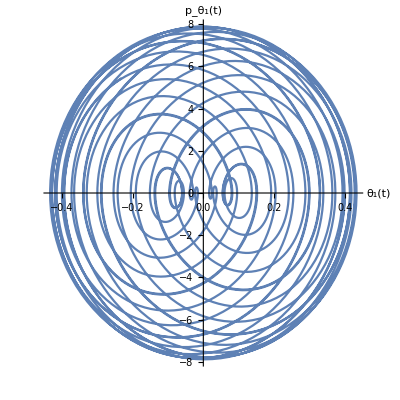

```mathematica
(*Tomamos un slice sobre el plano p, h y se grafica*)
ParametricPlot[Evaluate[{h[t], p[t]}/. sol],{t,0,50},AxesLabel->{"θ_1(t)","p_θ_1(t)"},  ImageSize->Full, AspectRatio->1]
```

```mathematica
(*Se hace el mismo proceso pero para theta_2 y su momento asociado*)
```

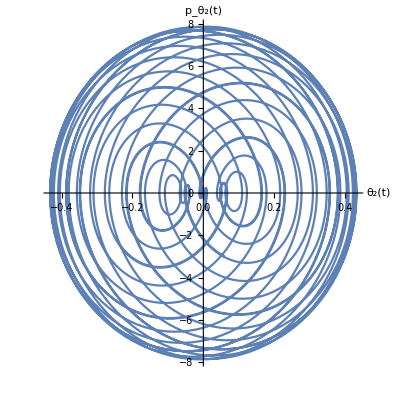

```mathematica
ParametricPlot[Evaluate[{j[t], q[t]}/. sol],{t,0,50},AxesLabel->{"θ_2(t)","p_θ_2(t)"},  ImageSize->Full, AspectRatio->1]
```

-Graphics3D-

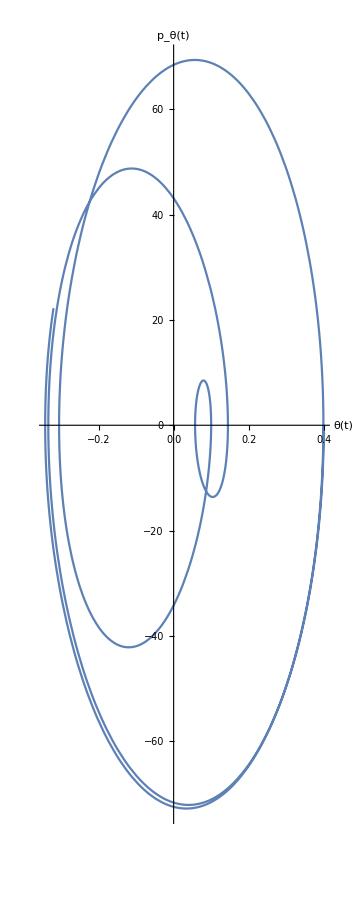

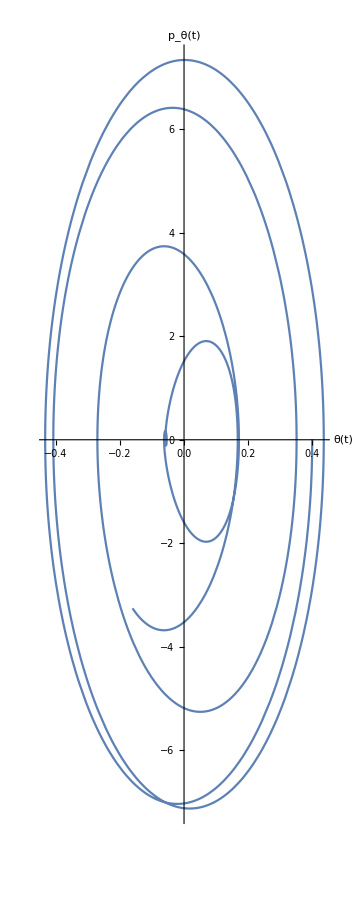

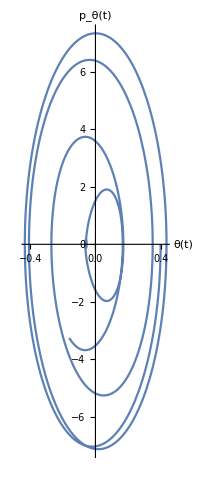

```mathematica
(*Se hace un corte a una hipersuperficie  para ver el comportamiento *)
ParametricPlot3D[Evaluate[{h[t],j[t], p[t]}/. sol],{t,0,50},AxesLabel->{"θ_1(t)","θ_2","p_θ_1(t)"},  ImageSize->Full, AspectRatio->1]
```